```mathematica
data1=ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\USA\\USA TV.txt",{Number,Number}];
data2=ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\USA\\USA TV (No Ny).txt",{Number,Number}];
data =ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\USA\\newUSA.txt",{Number,Number}];
```

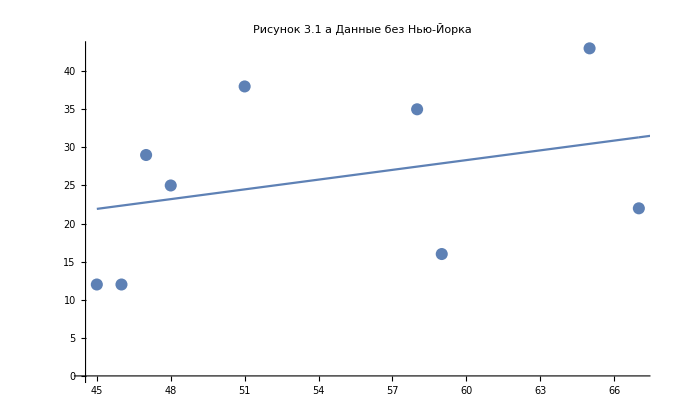

```mathematica
lp =ListPlot[{data2},PlotRange->All,PlotLabel->"Рисунок 3.1 а Данные без Нью-Йорка"];
llp=ListLinePlot[{data},PlotRange->All];
Show[lp,llp]
```

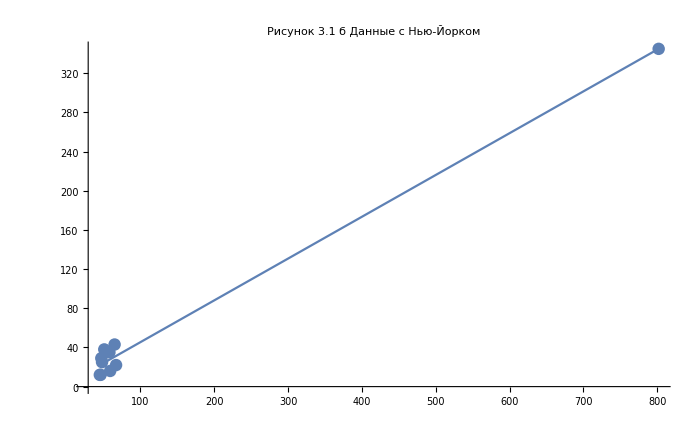

```mathematica
lp =ListPlot[{data1},PlotRange->All,PlotLabel->"Рисунок 3.1 б Данные с Нью-Йорком"];
llp=ListLinePlot[{data},PlotRange->All];
Show[lp,llp]
```